```mathematica
tf[a_,b_]:=Piecewise[{{0, ToString[a>b]=="False"}, {1, ToString[a>b]=="True"}}]
```

```mathematica
aa:=10000
Monitor[∑_(i=0)^aa ∑_(j=0)^aa tf[i,j],{i,j}]
∑_(i=0)^aa ∑_(j=0)^aa 1
```

50005000

100020001

```mathematica
50005000/100020001
```

```mathematica
N[5000/10001]
```

0.49995

```mathematica
500500
```

1002001

```mathematica
N[500500/1002001]
```

0.4995

```mathematica
ChineseRemainder[{1,2},{2,3}]
```

5

```mathematica
Reduce[ChineseRemainder[{a,c},{b,d}]  a<b&&c<d&&b≠d
```

```mathematica
ChineseRemainder[{1,2},{2,4}]
```

ChineseRemainder[{1,2},{2,4}]

```mathematica
MQ[a_,b_,c_,d_]:=Piecewise[{{{0,0}, (b>a&&d>c)==False}, {Piecewise[{{{0,1}, StringMatchQ[ToString[ChineseRemainder[{a,c},{b,d}]],NumberString]==False}, {{1,1}, StringMatchQ[ToString[ChineseRemainder[{a,c},{b,d}]],NumberString]==True}}], (b>a&&d>c)==True}}]
```

```mathematica
ab[{x_,y_}]:={x/y,N[x/y,100]}
```

```mathematica
MQ[1,2,2,3]
```

{1,1}

```mathematica
aa:=60
Monitor[Table[MQ[a,b,c,d],{a,1,aa},{b,1,aa},{c,1,aa},{d,1,aa}],{a,b,c,d}]
Partition[Flatten[%],2]
Total[%]
ab[%]//Column
```

```mathematica
{{1095083/1500625}, {0.729751270304039983340274885464389837567680133277800916284881299458558933777592669720949604331528529779258642232403165347771761765930862`100.}}
```

```mathematica
a mod b
c mod d
b*x+a==d*y+c
a<b&&c<d
Mod[a,GCD[b,d]]==GCD[c,GCD[b,d]]
```

```mathematica
a mod (a+b)
c mod (c+d)
(a+b)x+a==(c+d)y+c
(a+b)x-(c+d)y==c-a
c-a==k*GCD[a+b,c+d]==k*f==k*GCD[a,c]
a+b==ef
c+d==fg
GCD[e,f]==GCD[f,g]==GCD[e,g]==1
a mod f==c mod f
f*x+a==f*y+c
f*x-f*y==f(x-y)==c-a
x-y==k
GCD[a,b]==GCD[a+b,b]
c-a==k*GCD[a,c]
```

```mathematica
ac[a_,c_]:=Piecewise[{{0, ToString[Reduce[c-a==k*GCD[a,c],Integers]]=="False"}, {1, ToString[Reduce[c-a==k*GCD[a,c],Integers]]≠"False"}}]
```

```mathematica
aa:=100
Monitor[Total[Flatten[Table[ac[x,y],{x,1,aa},{y,1,aa}]]],{x,y}]
```

10000

```mathematica
gc[a_,b_]:=Piecewise[{{0, (GCD[a,b]==GCD[a+b,b])==False}, {1, (GCD[a,b]==GCD[a+b,b])==True}}]
```

```mathematica
aa:=1000
Monitor[Total[Flatten[Table[gc[x,y],{x,1,aa},{y,1,aa}]]],{x,y}]
```

1000000

```mathematica
GCD[a,b]==GCD[a±b,b]
```

```mathematica
GCD[131,331]
GCD[200,131]
GCD[131,69]
GCD[62,7]
GCD[55,7]
```

```mathematica
GCD[2k+1±2^n,2k+1]==1
```

```mathematica
GCD[2847372,5678903]
```

1

```mathematica
GCD[120,164]
GCD[44,120]
GCD[76,44]
32,44
12,32
12,20
8,12
4,8
4
```

```mathematica
(a+b)/b==a/b+b/b==a/b+1
```

```mathematica
k(GCD[a,b]==1⇔GCD[a±b,b]==1)
```

```mathematica
GCD[a,b]==1->GCD[ak,bk]==k
```

```mathematica
GCD[ak,bk]==GCD[ak±bk,bk]
```

```mathematica
GCD[q,w]==GCD[q±w,w]==GCD[Mod[a,b],b]
```

```mathematica
GCD[64,82]
GCD[18,64]
2*GCD[9,32]
2
```

2

2

2

«1 more identical outputs»

```mathematica
GCD[a^n,b^n]==(GCD[a,b])^n
```

```mathematica
√n==a/b∉Integers [GCD[a,b]==1&&n∈Integers]
n==(a^2/b^2) [GCD[a^2,b^2]==1]∴n∉Integers
```

```mathematica
GCD[567898765,45675]
```

35

```mathematica
Mod[567898765,45675]
```

```mathematica
Mod[45675,21490]
```

```mathematica
Mod[21490,2695]
```

```mathematica
Mod[2695,2625]
```

```mathematica
Mod[2625,70]
```

```mathematica
Mod[70,35]
```

0

```mathematica
GCD[a,b]->Mod[a,b]->Mod[b,Mod[a,b]]->Mod[Mod[a,b],Mod[b,Mod[a,b]]]
Subscript[r, 0]==b
Subscript[r, 1]==Mod[a,b]
Subscript[r, n+2]==Mod[Subscript[r, n],Subscript[r, n+1]]
```

```mathematica
RSolve[r[n+2]==Mod[r[n],r[n+1]],r[n],n]
```

RSolve[r[2+n]==Mod[r[n],r[1+n]],r[n],n]

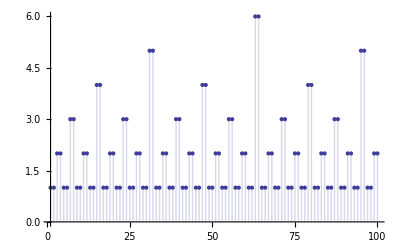

```mathematica
DiscretePlot[IntegerExponent[x^10+x^9+x^8+x^7+x^6+x^5+x^4+x^3+x^2+x,2],{x,1,100}]
```

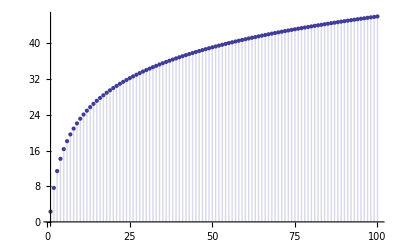

```mathematica
DiscretePlot[Log[x^10+x^9+x^8+x^7+x^6+x^5+x^4+x^3+x^2+x],{x,1,100}]
```

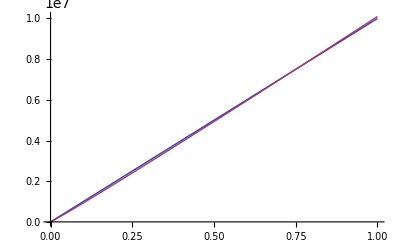

```mathematica
Plot[{x,(√x)/3.85 √Log[Gamma[x]]},{x,2,10000000}]
```

```mathematica
Reduce[(√x)/(385/100)√Log[y]==x,y,Reals]
```

(x==0&&y≥1)||(x≥0&&y==ⅇ^(5929 x/400))